# Critical points of multivariate rational functions

## Find and classify contributing critical points for ACSV

In progress. Based on examples and theory in Pemantle, Wilson, Melczer, Analytic Combinatorics in Several Variables (2nd edition), Cambridge University Press 2024.

## Definitions

```mathematica
Clear[asyVars, singEqs, singPts, smoothQ, varPtQ, gradLog, smoothPtQ, minimalPtQ, smoothFacQ, multiplePtNaiveQ,  smoothCritEqs, recenter, totalDeg, homogeneousPart, radical, hom, r ]; 

(* auxiliary functions *)
(* still may need to compute a standard factored form with H(0) = 1 *)

asyVars[F_]:= Array[r,Length[Variables[F]]];
gradLog[H_]:=-( Grad[H,Variables[H]]*Variables[H]);
recenter[H_,p_]:= H /. Inner[Rule, Variables[H], Map[#[[1]]+#[[2]] &, p], List]//Expand
totalDeg[H_]:= Module[{t}, Exponent[H /. (Thread[Variables[H]->t*ConstantArray[1,Length[Variables[H]]]]),t]];
radical[H_]:=Times @@ Map[#[[1]] &,FactorList[H]];
homogeneousPart[H_,d_]:=Module[{t},SeriesCoefficient[H/. Thread[Variables[H]->t*Variables[H]],{t,0,d}]/. t->1]
(* uses assumption that terms are sorted in increasing degree *)
hom[H_,p_]:= Module[{l}, l = Map[homogeneousPart[recenter[H,p],#] &, Range[0,totalDeg[H]]]; Select[l, !TrueQ[FullSimplify[# == 0]] &][[1]]]

(* classify  variety globally *)
singEqs[F_]:= Module[{t,H}, H = Denominator[F];  t = Grad[H, Variables[H]]; t = Append[t,H]];
singPts[F_]:=DeleteDuplicates[Solve[Map[#==0&,singEqs[F]],Variables[F]]];
smoothQ[F_]:=Length[singPts[F]]==0;
(* makes assumption - see usage *)
smoothFacQ[F_]:=Module[{H}, H = Denominator[F]; And @@ Map[smoothQ[Numerator[F]/#[[1]]] &, Delete[FactorList[H], 1]] ]; 

(* classify point on variety *)
varPtQ[F_, p_]:= Module[{H}, H = Denominator[F];(H /. p) == 0];
smoothPtQ[F_, p_]:= Module[{H}, H = Denominator[F];varPtQ[F,p] && (!And @@ Map[#==0 &, gradLog[H]/.p])];
multiplePtNaiveQ[F_,p_]:= varPtQ[F,p] && smoothFacQ[F];
minimalPtQ[F_,p_]:= varPtQ[F,p] && Module[{a,t, H},H = Denominator[F];t=Solve[(H/. Thread[Variables[H]->a*Abs[Variables[H]]] /. p)==0 && 0<=a<1, a, Reals]; Length[t]==0];

(* critical points *)
smoothCritEqs[F_]:= Module[{t,H}, H = Denominator[F]; t = gradLog[H]*asyVars[H];
t = t -t[[1]]; t[[1]] = H; t];
Attributes[smoothCritEqs]:=Listable;
```

## Documentation

### Usage

Throughout, F = G/H where G, H are coprime polynomials and  V = V[H] is the variety H=0. Typically F is a power series and has all nonnegative coefficients (“combinatorial case”). None of the functions have any optional arguments. Note that replacing H with the radical of H (product of all distinct  irreducible factors) gives the same variety, so we preprocess first.

```mathematica
H = (1 - x - y - x*y)*(1 - x - y)^2
G = 1
H = radical[H]
F = G/H
```

(1-x-y)^2 (1-x-y-x y)

1

-((-1+x+y) (-1+x+y+x y))

-1/((-1+x+y) (-1+x+y+x y))

```mathematica
(* asyVars[H] outputs variables r[1], ... r[d] when H has d variables *)
asyVars[H]
```

{r[1],r[2]}

```mathematica
(* gradLog[H] outputs the logarithmic gradient[xD[H,x],yD[H,y],...]*)
gradLog[H]
```

{-x (1-x-y-x y-(1+y) (-1+x+y)),-y (1-x-y-x y-(1+x) (-1+x+y))}

```mathematica
(* recenter[H,p] changes variable additively so that p is the origin and expresses H in new variables (note they are same as old variables) *)
p = {x->Sqrt[2]-1, y->Sqrt[2]-1}
recenter[H,p]
```

{x→-1+√2,y→-1+√2}

-4 x+3 √2 x-√2 x^2-4 y+3 √2 y+3 x y-4 √2 x y-x^2 y-√2 y^2-x y^2

```mathematica
(* totalDeg[H] gives the total degree of the polynomial H*)
totalDeg[H]
```

3

```mathematica
(* homogeneousPart[H,d] outputs homogeneous part of total degree d of H*)
Map[homogeneousPart[recenter[H,p],#] &, Range[0,4]]
```

{0,-4 x+3 √2 x-4 y+3 √2 y,-√2 x^2+3 x y-4 √2 x y-√2 y^2,-x^2 y-x y^2,0}

```mathematica
(* hom[H,p] outputs lowest degree homogeneous part of H recentered at p *)
hom[H,p]
```

-4 x+3 √2 x-4 y+3 √2 y

```mathematica
(* singEqs[F] outputs the list LHS of the equations whose solutions give all singular points of V *)
singEqs[F]
```

{-1+x+y+x y+(1+y) (-1+x+y),-1+x+y+x y+(1+x) (-1+x+y),(-1+x+y) (-1+x+y+x y)}

```mathematica
(* singPts[F] outputs the singular points of V,the solutions of singEqs[F] *)
singPts[F]
```

{{x→0,y→1},{x→1,y→0}}

```mathematica
(* smoothQ[F] outputs whether V is smooth (has no singular points) *)
smoothQ[F]
```

False

```mathematica
(* smoothFacQ[F] outputs whether the polynomial factorization of H is into smooth factors (assumes constant factor is always the first in the factorization)*)
smoothFacQ[F]
```

True

```mathematica
(* varPtQ[F,p] outputs whether p lies on V *)
varPtQ[F,p]
```

True

```mathematica
(* smoothPtQ[F,p] outputs whether p is a smooth point of V *)
smoothPtQ[F,p]
```

True

```mathematica
(* multiplePtNaiveQ[F,p] outputs whether p is an obviously multiple point because the algebraic global factorization suffices *)
multiplePtNaiveQ[F,p]
```

True

```mathematica
(* minimalPtQ[F,p] outputs whether the point p is a minimal point of V (only used in the combinatorial power series case) *)
minimalPtQ[F,p]
```

True

```mathematica
(* smoothCritEqs[F] outputs the list of LHS of critical point equations for the top stratum *)
smoothCritEqs[F]
```

{(-1+x+y) (-1+x+y+x y),x (-1+x+y+x y+(1+y) (-1+x+y)) r[1]-y (-1+x+y+x y+(1+x) (-1+x+y)) r[2]}

## Worked Examples

### Simple example

```mathematica
H = 1 - x - y - x*y; G = 1; H = radical[H]; F = G/H
```

1/(1-x-y-x y)

```mathematica
alpha = {2,3}
```

{2,3}

```mathematica
smoothQ[F]
```

True

```mathematica
smoothCritEqs[F]
```

{1-x-y-x y,x (-1-y) r[1]-(-1-x) y r[2]}

```mathematica
s = Solve[Map[#==0&,smoothCritEqs[F]],Variables[F]]
```

{{x→(-r[1]-√(r[1]^2+r[2]^2))/r[2],y→(-r[2]-√(r[1]^2+r[2]^2))/r[1]},{x→(-r[1]+√(r[1]^2+r[2]^2))/r[2],y→(-r[2]+√(r[1]^2+r[2]^2))/r[1]}}

```mathematica
s1 =( s /. Thread[asyVars[F] -> alpha])
```

{{x→1/3 (-2-√13),y→1/2 (-3-√13)},{x→1/3 (-2+√13),y→1/2 (-3+√13)}}

```mathematica
Map[minimalPtQ[F,#] &, s1]
```

{False,True}

### Another example

```mathematica
H = 1-x-y - y^5; G = 1; H = radical[H]; F=G/H
```

1/(1-x-y-y^5)

```mathematica
smoothQ[F]
```

True

```mathematica
smoothCritEqs[F]
```

{1-x-y-y^5,-x r[1]-y (-1-5 y^4) r[2]}

```mathematica
s = Solve[Map[#==0&,smoothCritEqs[F]],Variables[F]]
```

{{x→(5 r[2]-4 r[2] Root[-r[1]+(r[1]+r[2]) #1+(r[1]+5 r[2]) #1^5&,1])/(r[1]+5 r[2]),y→Root[-r[1]+(r[1]+r[2]) #1+(r[1]+5 r[2]) #1^5&,1]},{x→(5 r[2]-4 r[2] Root[-r[1]+(r[1]+r[2]) #1+(r[1]+5 r[2]) #1^5&,2])/(r[1]+5 r[2]),y→Root[-r[1]+(r[1]+r[2]) #1+(r[1]+5 r[2]) #1^5&,2]},{x→(5 r[2]-4 r[2] Root[-r[1]+(r[1]+r[2]) #1+(r[1]+5 r[2]) #1^5&,3])/(r[1]+5 r[2]),y→Root[-r[1]+(r[1]+r[2]) #1+(r[1]+5 r[2]) #1^5&,3]},{x→(5 r[2]-4 r[2] Root[-r[1]+(r[1]+r[2]) #1+(r[1]+5 r[2]) #1^5&,4])/(r[1]+5 r[2]),y→Root[-r[1]+(r[1]+r[2]) #1+(r[1]+5 r[2]) #1^5&,4]},{x→(5 r[2]-4 r[2] Root[-r[1]+(r[1]+r[2]) #1+(r[1]+5 r[2]) #1^5&,5])/(r[1]+5 r[2]),y→Root[-r[1]+(r[1]+r[2]) #1+(r[1]+5 r[2]) #1^5&,5]}}

```mathematica
alpha = {2,3}; s1 =  s /. Thread[asyVars[H] -> alpha]
```

{{x→1/17 (15-12 ),y→},{x→1/17 (15-12 ),y→},{x→1/17 (15-12 ),y→},{x→1/17 (15-12 ),y→},{x→1/17 (15-12 ),y→}}

```mathematica
s2 = s1//N
```

{{x→0.61776,y→0.37484},{x→1.30601+0.376295 ⅈ,y→-0.600188-0.533085 ⅈ},{x→1.30601-0.376295 ⅈ,y→-0.600188+0.533085 ⅈ},{x→0.590987+0.397228 ⅈ,y→0.412768-0.562739 ⅈ},{x→0.590987-0.397228 ⅈ,y→0.412768+0.562739 ⅈ}}

```mathematica
m = Map[minimalPtQ[F,#] &, s1] //FullSimplify
```

{True,False,False,False,False}

### Harder example - polyominoes

```mathematica
H = (1-x)^4-x*y*(1-x-x^2+x^3+x^2*y); G=1; F=G/H
```

1/((1-x)^4-x y (1-x-x^2+x^3+x^2 y))

```mathematica
alpha = {2,3}
```

{2,3}

```mathematica
smoothQ[F]
```

False

```mathematica
singPts[F]
```

{{x→1,y→0}}

```mathematica
smoothFacQ[F]
```

False

```mathematica
s = Solve[Map[#==0&,smoothCritEqs[F]],Variables[F]];
```

```mathematica
s1 = s /. Thread[asyVars[H] -> alpha];
```

```mathematica
s2 = s1//N
```

{{x→1.,y→0.},{x→-6.57163,y→2.25055},{x→0.137151,y→4.35273},{x→-0.116094-0.245945 ⅈ,y→12.6984+13.1626 ⅈ},{x→-0.116094+0.245945 ⅈ,y→12.6984-13.1626 ⅈ}}

```mathematica
Map[minimalPtQ[F,#] &, s2]
```

{True,False,False,False,False}

```mathematica
m = Map[minimalPtQ[F,#] &, s1] //FullSimplify
```

{True,False,True,False,False}

### Example where naive methods fail, and local factoring is needed s

```mathematica
H = 19 -20*x - 20*y + 5*(x^2+y^2)+14*x*y - 2*(x^2*y+x*y^2)+x^2*y^2; G=1; Hh = radical[H]; F=G/H
```

1/(19-20 x-20 y+14 x y+x^2 y^2+5 (x^2+y^2)-2 (x^2 y+x y^2))

```mathematica
smoothQ[F]
```

False

```mathematica
GroebnerBasis[singEqs[F], Variables[F]]
```

{-1+y,-1+x}

```mathematica
sol = Solve[Map[#==0 &, singEqs[F]], Variables[F]]
```

{{x→1,y→1}}

```mathematica
p = Map[#[[2]] &, sol[[1]]]
```

{1,1}

```mathematica
Factor[H]
```

19-20 x+5 x^2-20 y+14 x y-2 x^2 y+5 y^2-2 x y^2+x^2 y^2

```mathematica
Factor[H, Extension -> Automatic]
```

19-20 x+5 x^2-20 y+14 x y-2 x^2 y+5 y^2-2 x y^2+x^2 y^2

```mathematica
smoothFacQ[F]
```

False

```mathematica
smoothPtQ[F,Thread[Variables[H]->p]]
```

False

```mathematica
multiplePtNaiveQ[F, Thread[Variables[H]->p]]
```

False

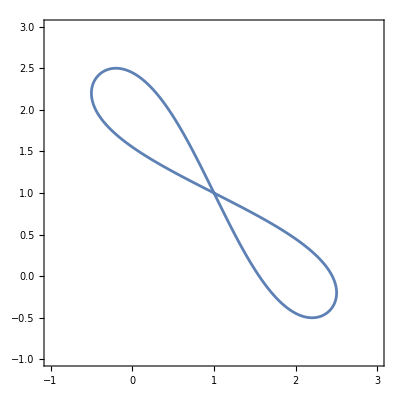

```mathematica
ContourPlot[H==0,{x,-1,3},{y,-1,3}, PlotPoints -> 200]
```

```mathematica
Normal[Series[(1/H), {x,0,3}, {y,0,3}] ]
```

1/19+(20 y)/361+(305 y^2)/6859+(4200 y^3)/130321+x (20/361+(534 y)/6859+(10282 y^2)/130321+(172220 y^3)/2476099)+x^2 (305/6859+(10282 y)/130321+(233307 y^2)/2476099+(4468316 y^3)/47045881)+x^3 (4200/130321+(172220 y)/2476099+(4468316 y^2)/47045881+(95135680 y^3)/893871739)

```mathematica
ResourceFunction["MultivariateTaylorPolynomial"][1/(19-20 x-20 y+14 x y+x^2 y^2+5 (x^2+y^2)-2 (x^2 y+x y^2)),{x,y},4]
```

1/19+(20 (x+y))/361+(305 x^2+534 x y+305 y^2)/6859+(2 (2100 x^3+5141 x^2 y+5141 x y^2+2100 y^3))/130321+(55025 x^4+172220 x^3 y+233307 x^2 y^2+172220 x y^3+55025 y^4)/2476099

```mathematica
ysols = Solve[H==0, y]
```

{{y→(10-7 x+x^2-√(5-2 x-15 x^2+16 x^3-4 x^4))/(5-2 x+x^2)},{y→(10-7 x+x^2+√(5-2 x-15 x^2+16 x^3-4 x^4))/(5-2 x+x^2)}}

```mathematica
Map[Series[#, {x,0,4}] & ,ysols /. Rule->(#2&)] //N
```

{{1.55279-0.689443 (x+0.)+0.29343 (x+0.)^2-0.324328 (x+0.)^3+0.391171 (x+0.)^4+O[x+0.]^5},{2.44721-0.510557 (x+0.)-1.17343 (x+0.)^2+0.212328 (x+0.)^3-0.259971 (x+0.)^4+O[x+0.]^5}}

```mathematica
Factor[hom[H,p]]
```

2 (2 x+y) (x+2 y)

```mathematica
H = (1-x-y)^2
```

(1-x-y)^2

```mathematica
ApartSquareFree[1/H]
```

1/(-1+x+y)^2

```mathematica
radical[H]
```

-1+x+y